{a_0→-5,a_1→10,a_2→1}

-5+10 x+x^2

-5+10 x+x^2

True

{True,True,True}

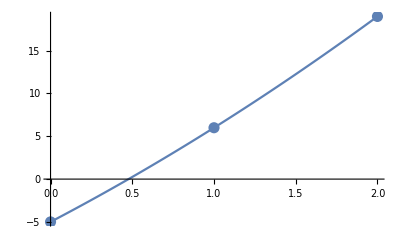

```mathematica
X={0,1,2}; F= {-5,6,19};
n=Length[X]-1;
Do[{Subscript[x, i]=X[[i+1]],Subscript[f, i]=F[[i+1]]},{i,0,n}]
koef=Solve[Table[Subscript[a, 0]+∑_(k=1)^n Subscript[a, k] Subscript[x, j]^k==Subscript[f, j],{j,0,n}],{}][[1]]
P[x_]=∑_(k=0)^n Subscript[a, k] x^k//.koef
Tbl=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
P1[x_]=InterpolatingPolynomial[Tbl, x]//Expand
P[x]==P1[x]
Table[P[Subscript[x, i]]==Subscript[f, i],{i,0,n}]
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1, Gr2]
```